f[2]:

1.

f[3]:

2.

f[4]:

3.

f[5]:

5.

f[6]:

8.

f[7]:

13.

f[8]:

21.

f[9]:

34.

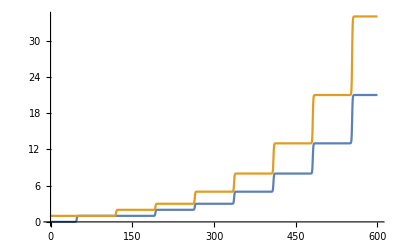

```mathematica
rsys={
    DiscreteInitCMP[],
    MakeOscillatorSpecies[2],
    conc[f0,0],
    conc[f1,1],
    phase[1,{
        DiscreteLd[f0,f0tmp],
        DiscreteLd[f1,f1tmp]
    }],
    phase[2,{
        DiscreteAdd[f0tmp,f1tmp,f1],
        DiscreteLd[f1tmp,f0]
    }]
};
tmax=600;
sol=SimulateRxnsys[rsys, tmax];
Print["f[2]:"];
EvaluateRxnAtPoint[sol,f1,80]
Print["f[3]:"];
EvaluateRxnAtPoint[sol,f1,150]
Print["f[4]:"];
EvaluateRxnAtPoint[sol,f1,250]
Print["f[5]:"];
EvaluateRxnAtPoint[sol,f1,300]
Print["f[6]:"];
EvaluateRxnAtPoint[sol,f1,380]
Print["f[7]:"];
EvaluateRxnAtPoint[sol,f1,430]
Print["f[8]:"];
EvaluateRxnAtPoint[sol,f1,520]
Print["f[9]:"];
EvaluateRxnAtPoint[sol,f1,600]
Plot[Evaluate[{f0[t],f1[t]}/.sol],{t,0,tmax},PlotRange->{0,All}]
```